## Метод серединных квадратов

```mathematica
findperiod=Module[{b,c=1},While[Length[b=Union@Partition[#,c,c,{1,1},Take[#,c]]]>1,c++];
{Length@First@b,First@b}]&;
```

```mathematica
Clear[generateFonNeyman]
generateFonNeyman[R0_,amount_]:=Module[{n=Length[IntegerDigits[R0]],x=R0,value},
Do[value=FromDigits[IntegerDigits[x^2,10,2n]⟦n/2+1;;-n/2-1⟧];x=value;i;If[x==0,Break[]];Sow[value/N[10^n]],{i,amount}]]
```

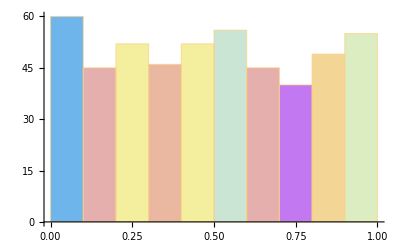

<|Mean→0.491696,Variance→0.0871537|>

```mathematica
result=Reap[generateFonNeyman[R0=11348686,amount=500]]⟦2⟧[[1]];
Histogram[result,ChartBaseStyle->EdgeForm[Dotted],ColorFunction->"Pastel"]
<|"Mean"->Mean[result],"Variance"->Variance[result]|>
```

```mathematica
{Length@FindRepeat[result],findperiod[result][[1]]}
```

{500,500}

## Метод серединных произведений

```mathematica
Clear[generateMultiplyMethod]
generateMultiplyMethod[R0_,R1_,amount_]:=Module[{n=Length[IntegerDigits[R0]],x1=R0,x2=R1,dig},
Table[dig=IntegerDigits[x1*x2,10,2n];x1=x2;x2=FromDigits[dig⟦n/2+1;;-n/2-1⟧];x2/N[10^n],{i,amount}]]
```

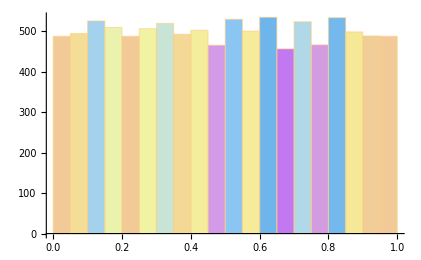

<|Mean→0.498645,Variance→0.0828355|>

```mathematica
result=generateMultiplyMethod[R0=333333,R1=333322,amount=10000];
Histogram[result,ChartBaseStyle->EdgeForm[Dotted],ColorFunction->"Pastel"]
<|"Mean"->Mean[result],"Variance"->Variance[result]|>
```

```mathematica
{Length@FindRepeat[result],findperiod[result][[1]]}
```

{10000,10000}

## Линейный конгруэнтный датчик

```mathematica
Clear[generateCongruentialMethod]
generateCongruentialMethod[k_,b_,M_,R0_,amount_]:=Module[{x1=R0},
Table[x1=Mod[k*x1+b,M];N[x1/M],{i,amount}]]
```

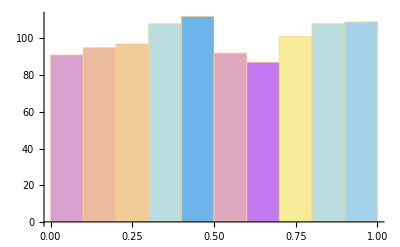

<|Mean→0.510531,Variance→0.084228|>

```mathematica
result=generateCongruentialMethod[k=106,b=1283,M=6075,R0=1,amount=1000];
result2=generateCongruentialMethod[k=936,b=1399,M=6655,R0=1,amount=1000];
Histogram[result,ChartBaseStyle->EdgeForm[Dotted],ColorFunction->"Pastel"]
<|"Mean"->Mean[result],"Variance"->Variance[result]|>
```

```mathematica
{Length@FindRepeat[result],findperiod[result][[1]]}
```

{1000,1000}

```mathematica
PearsonChiSquareTest[result,UniformDistribution[{0,1}]]
```

0.562984

## Преобразование Бокса-Мюллера: U[0,1] → Ν(0,1)

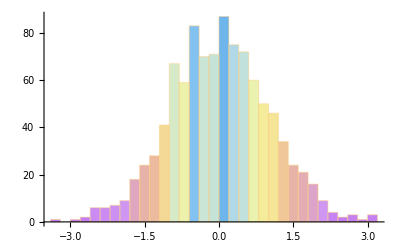

```mathematica
normal = Cos[2*π*result]*√(-2Log[result2]);
Histogram[normal,ChartBaseStyle->EdgeForm[Dotted],ColorFunction->"Pastel"]
```

p-value

```mathematica
KolmogorovSmirnovTest[normal,NormalDistribution[0,1]]
```

0.88096

```mathematica
PearsonChiSquareTest[normal,NormalDistribution[0,1]]
```

0.941779